# LOAD DATA

```mathematica
SetDirectory[NotebookDirectory[]];
filenames = {"M_SD_001","M_SD_002","M_SD_003","M_SD_008","M_SD_009","M_SD_011","M_SD_014","M_SD_015","M_SD_017","M_SD_021","M_SD_023","M_SD_031","M_SD_032","M_SD_033","M_SD_010","M_SD_012","M_SD_013","M_SD_020","M_SD_024","M_SD_025","M_SD_026","M_SD_027","M_SD_028","M_SD_029","M_SD_030","M_PL_069_03","M_PL_036","M_PL_069_01","M_PL_067","M_PL_032","M_PL_050","M_PL_071","M_PL_025","M_PL_003","M_PL_039","M_PL_006","M_PL_008","M_PL_011","M_PL_013","M_PL_033","M_PL_037","M_PL_038","M_PL_046","M_PL_059","M_PL_063","M_PL_064","M_PL_065","M_PL_066","M_PL_068","M_PL_069_02","M_PL_070"};
NetsN = Length@filenames;
```

```mathematica
EWS = Table[Table[Import["data_GeneralFigs/"<>j<>"EWS"<>ToString[i]<>".csv","Table"],{i,0,18}],{j,filenames⟦1;;51⟧}];
```

```mathematica
SS = Import["data_GeneralFigs/SSall.mx"];
Deg = Import["data_GeneralFigs/Degree.mx"];
MSSsize =  Import["data_GeneralFigs/MSSsize.mx"];
MaxSS = Import["data_GeneralFigs/MaxSS.csv"]//Flatten;
DevEq = Import["data_GeneralFigs/DevEq2.csv"]//Flatten;
rData=Import["data_GeneralFigs/Zrd.csv" ]//Flatten;
qData=Import["data_GeneralFigs/Zqd.csv" ]//Flatten;
```

```mathematica
SkewnessSS = Table[
Skewness[SS⟦network⟧]
,{network, 1, Length@SS}];
ρq = DevEq;
```

# FUNCTIONS

## Functions to calculate r_1

Returns Quantiles {1/4, 1/2, 3/4} of r_1 (i.e., the early-warning score ratio of choosing one species)

```mathematica
CalculateRsensor[networkID_, numberofsamples_,  ϵ_]:=Module[{EWnom,SensorScore,vertexDegree,n,dataS,orderS,orderR,r1,numrandom},
EWnom=Table[EWS⟦networkID⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦networkID⟧}];
SensorScore = SS⟦networkID⟧;
vertexDegree=Deg⟦networkID⟧;
n = Length@SensorScore;

dataS=Table[
ParallelTable[
orderS = Reverse@Ordering[SensorScore+RandomReal[{-ϵ,ϵ}, Length@SensorScore]]; (* by sensor*)
orderR = RandomSample[Range@Length@EWnom⟦1⟧, Length@EWnom⟦1⟧];  (* at random*)
r1=Take[EWnom⟦i⟧⟦orderS⟧,1]/Max@EWnom⟦i⟧;
r1
,{k,1,numberofsamples}]//Flatten
,{i,1,Length@EWnom}]//Flatten;

Quantile[dataS,{1/4,1/2,3/4}]//N
]

CalculateRdegree[networkID_, numberofsamples_,  ϵ_]:=Module[{EWnom,SensorScore,vertexDegree,n,dataD,orderD,orderR,r1,numrandom},
EWnom=Table[EWS⟦networkID⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦networkID⟧}];
SensorScore = SS⟦networkID⟧;
vertexDegree=Deg⟦networkID⟧;
n = Length@SensorScore;

dataD=Table[
ParallelTable[
orderD = Ordering[vertexDegree+RandomReal[{-0.3,0.3}, Length@vertexDegree]]; (* by degree*)
orderR = RandomSample[Range@Length@EWnom⟦1⟧, Length@EWnom⟦1⟧];  (* at random*)
r1=Take[EWnom⟦i⟧⟦orderD⟧,1]/Max@EWnom⟦i⟧;
r1
,{k,1,numberofsamples}]//Flatten
,{i,1,Length@EWnom}]//Flatten;

Quantile[dataD,{1/4,1/2,3/4}]//N
]

CalculateRrand[networkID_, numberofsamples_,  ϵ_]:=Module[{EWnom,SensorScore,vertexDegree,n,dataD,orderD,orderR,r1,numrandom},
EWnom=Table[EWS⟦networkID⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦networkID⟧}];
SensorScore = SS⟦networkID⟧;
vertexDegree=Deg⟦networkID⟧;
n = Length@SensorScore;

dataD=Table[
ParallelTable[
orderD = Ordering[vertexDegree+RandomReal[{-0.3,0.3}, Length@vertexDegree]]; (* by degree*)
orderR = RandomSample[Range@Length@EWnom⟦1⟧, Length@EWnom⟦1⟧];  (* at random*)
r1=Take[EWnom⟦i⟧⟦orderR⟧,1]/Max@EWnom⟦i⟧;
r1
,{k,1,numberofsamples}]//Flatten
,{i,1,Length@EWnom}]//Flatten;

Quantile[dataD,{1/4,1/2,3/4}]//N
]
```

## Functions to calculate q^*

Returns Quantiles {1/4, 1/2, 3/4} of q^*

```mathematica
CalculateQsensor[networkID_, numberofsamples_,  ϵ_]:=Module[{EWnom,SensorScore,vertexDegree,n,dataS,orderS,orderR,numsensor,numrandom},
EWnom=Table[EWS⟦networkID⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦networkID⟧}];
SensorScore = SS⟦networkID⟧;
vertexDegree=Deg⟦networkID⟧;
n = Length@SensorScore;

dataS=Table[
ParallelTable[
orderS = Reverse@Ordering[SensorScore+RandomReal[{-ϵ,ϵ}, Length@SensorScore]]; (* by sensor*)
orderR = RandomSample[Range@Length@EWnom⟦1⟧, Length@EWnom⟦1⟧];  (* at random*)
numsensor=FirstPosition[Round[#,0.0001],1.]&@Table[
Max@Take[EWnom⟦i⟧⟦orderS⟧,size]/Max@EWnom⟦i⟧
,{size, 1,Length@EWnom⟦i⟧}];
numsensor
,{k,1,numberofsamples}]//Flatten
,{i,1,Length@EWnom}]//Flatten;

Quantile[dataS/n,{1/4,1/2,3/4}]//N
]

CalculateQdegree[networkID_, numberofsamples_,  ϵ_]:=Module[{EWnom,SensorScore,vertexDegree,n,dataD,orderD,orderR,numsensor,numrandom},
EWnom=Table[EWS⟦networkID⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦networkID⟧}];
SensorScore = SS⟦networkID⟧;
vertexDegree=Deg⟦networkID⟧;
n = Length@SensorScore;

dataD=Table[
ParallelTable[
orderD = Ordering[vertexDegree+RandomReal[{-0.3,0.3}, Length@vertexDegree]]; (* by degree*)
orderR = RandomSample[Range@Length@EWnom⟦1⟧, Length@EWnom⟦1⟧];  (* at random*)
numsensor=FirstPosition[Round[#,0.0001],1.]&@Table[
Max@Take[EWnom⟦i⟧⟦orderD⟧,size]/Max@EWnom⟦i⟧
,{size, 1,Length@EWnom⟦i⟧}];
numsensor
,{k,1,numberofsamples}]//Flatten
,{i,1,Length@EWnom}]//Flatten;

Quantile[dataD/n,{1/4,1/2,3/4}]//N
]

CalculateQrand[networkID_, numberofsamples_,  ϵ_]:=Module[{EWnom,SensorScore,vertexDegree,n,dataD,orderD,orderR,numsensor,numrandom},
EWnom=Table[EWS⟦networkID⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦networkID⟧}];
SensorScore = SS⟦networkID⟧;
vertexDegree=Deg⟦networkID⟧;
n = Length@SensorScore;

dataD=Table[
ParallelTable[
orderD = Ordering[vertexDegree+RandomReal[{-0.3,0.3}, Length@vertexDegree]]; (* by degree*)
orderR = RandomSample[Range@Length@EWnom⟦1⟧, Length@EWnom⟦1⟧];  (* at random*)
numrandom=FirstPosition[Round[#,0.0001],1.]&@Table[
Max@Take[EWnom⟦i⟧⟦orderR⟧,size]/Max@EWnom⟦i⟧
,{size, 1,Length@EWnom⟦i⟧}];
numrandom
,{k,1,numberofsamples}]//Flatten
,{i,1,Length@EWnom}]//Flatten;

Quantile[dataD/n,{1/4,1/2,3/4}]//N
]
```

Returns the Quantiles {1/4, 1/2, 3/4} of  q^*-(q^*)_rand. Here q^* is the fraction of species that we need to measure to get the earliest detection of the transition

```mathematica
CalculateDeltaQsensor[networkID_, numberofsamples_,  ϵ_]:=Module[{EWnom,SensorScore,vertexDegree,n,dataS,orderS,orderR,numsensor,numrandom},
EWnom=Table[EWS⟦networkID⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦networkID⟧}];
SensorScore = SS⟦networkID⟧;
vertexDegree=Deg⟦networkID⟧;
n = Length@SensorScore;

dataS=Table[
ParallelTable[
orderS = Reverse@Ordering[SensorScore+RandomReal[{-ϵ,ϵ}, Length@SensorScore]]; (* by sensor*)
orderR = RandomSample[Range@Length@EWnom⟦1⟧, Length@EWnom⟦1⟧];  (* at random*)
numsensor=FirstPosition[Round[#,0.0001],1.]&@Table[
Max@Take[EWnom⟦i⟧⟦orderS⟧,size]/Max@EWnom⟦i⟧
,{size, 1,Length@EWnom⟦i⟧}];
numrandom=FirstPosition[Round[#,0.0001],1.]&@Table[
Max@Take[EWnom⟦i⟧⟦orderR⟧,size]/Max@EWnom⟦i⟧
,{size, 1,Length@EWnom⟦i⟧}];
numsensor-numrandom
,{k,1,numberofsamples}]//Flatten
,{i,1,Length@EWnom}]//Flatten;

Quantile[dataS/n,{1/4,1/2,3/4}]//N
]

CalculateDeltaQdegree[networkID_, numberofsamples_,  ϵ_]:=Module[{EWnom,SensorScore,vertexDegree,n,dataD,orderD,orderR,numsensor,numrandom},
EWnom=Table[EWS⟦networkID⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦networkID⟧}];
SensorScore = SS⟦networkID⟧;
vertexDegree=Deg⟦networkID⟧;
n = Length@SensorScore;

dataD=Table[
ParallelTable[
orderD = Ordering[vertexDegree+RandomReal[{-0.3,0.3}, Length@vertexDegree]]; (* by degree*)
orderR = RandomSample[Range@Length@EWnom⟦1⟧, Length@EWnom⟦1⟧];  (* at random*)
numsensor=FirstPosition[Round[#,0.0001],1.]&@Table[
Max@Take[EWnom⟦i⟧⟦orderD⟧,size]/Max@EWnom⟦i⟧
,{size, 1,Length@EWnom⟦i⟧}];
numrandom=FirstPosition[Round[#,0.0001],1.]&@Table[
Max@Take[EWnom⟦i⟧⟦orderR⟧,size]/Max@EWnom⟦i⟧
,{size, 1,Length@EWnom⟦i⟧}];
numsensor-numrandom
,{k,1,numberofsamples}]//Flatten
,{i,1,Length@EWnom}]//Flatten;

Quantile[dataD/n,{1/4,1/2,3/4}]//N
]
```

# ANALYSIS

## Fig S6 (Size of the MSS)

Fraction of the MSS

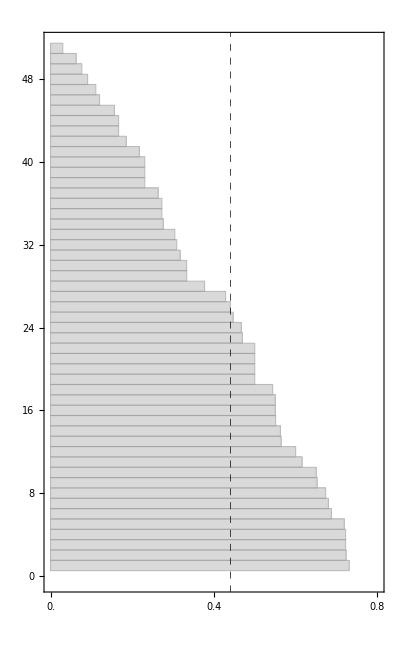

```mathematica
Length[#]&/@SS;
MSSsize/.{0->1};
fMSS=(MSSsize/.{0->1})/(Length[#]&/@SS)//N;

networkorder = Reverse@Ordering@fMSS;

BarChart[fMSS⟦networkorder⟧,
AspectRatio->GoldenRatio,
Frame->True,
GridLines->{{Median@fMSS},{}},
GridLinesStyle->Directive[Dashed,Black],
PlotRange->{{0,0.8},Automatic},
FrameTicks->{{All,None},{Range[0,1,0.2],None}},
ChartStyle->Directive[LightGray, EdgeForm[Gray]],
ImageSize->{Automatic,300},
 BarOrigin->Left]

{100*Min@fMSS,100*Max@fMSS, 100*Median@fMSS};
```

## Fig 4a (Fraction of species that do not anticipate the transition)

```mathematica
network = 6;

data=Table[
EWnom=Table[EWS⟦network⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦network⟧}];

SensorScore = SS⟦network⟧;
vertexDegree=Deg⟦network⟧;
medianEW = Median@EWnom;

temp=Table[
Count[EWnom⟦i⟧,0.]/Length@medianEW//N
,{i,1,Length@EWnom}]
,{network,1,Length@EWS}];

dataNoWarning=data//Flatten;
```

```mathematica
Median@data
```

{0.128205,0.125,0.137931,0.125,0.151515,0.15625,0.15,0.148936,0.125,0.12,0.15625,0.140351,0.15,0.153846,0.153846,0.15,0.152174,0.138462,0.14}

Fraction of species that are δ-close to w_max.

```mathematica
δ=0;
dataBestWarning=Table[
EWnom=Table[EWS⟦network⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦network⟧}];

SensorScore = SS⟦network⟧;
vertexDegree=Deg⟦network⟧;
medianEW = Median@EWnom;

temp=Table[
Count[EWnom⟦i⟧/Max@EWnom⟦i⟧,x_/;x≥1-δ]/Length@EWnom⟦i⟧//N
,{i,1,Length@EWnom}]
,{network,1,Length@EWS}]//Flatten;

δ=0.5;
dataDeltaWarning=Table[
EWnom=Table[EWS⟦network⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦network⟧}];

SensorScore = SS⟦network⟧;
vertexDegree=Deg⟦network⟧;
medianEW = Median@EWnom;

temp=Table[
Count[EWnom⟦i⟧/Max@EWnom⟦i⟧,x_/;x≥1-δ]/Length@EWnom⟦i⟧//N
,{i,1,Length@EWnom}]
,{network,1,Length@EWS}]//Flatten;
```

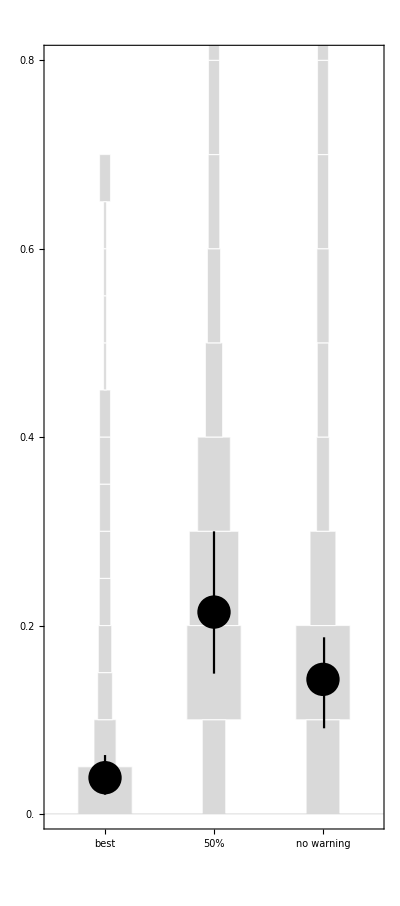

{0.142857,0.0384615}

```mathematica
Show[
DistributionChart[{dataBestWarning,dataDeltaWarning,dataNoWarning},
ChartElementFunction->"HistogramDensity",
ImageSize->{Automatic,230},
PlotRange->{{0.5,3.5},{0,0.8}},
GridLines->{{},{0}},
Frame->{False, True, False, False},
FrameTicks->{{Range[-1,1,0.2],None},{Automatic,None}},
FrameTicksStyle->11,
ChartStyle->{{EdgeForm[White],EdgeForm[White]},{LightGray,LightGray,LightGray}},
AspectRatio->1.4GoldenRatio,
ChartLabels->{"best","50%","no warning"}
]
(*,
ListPlot[Thread[{3+RandomReal[{-0.3,0.3},Length@dataNoWarning],dataNoWarning}],
PlotStyle->Directive[PointSize[0.01],Opacity[0.2],Gray]
]
,
ListPlot[Thread[{2+RandomReal[{-0.3,0.3},Length@dataBestWarning],dataNoWarning}],
PlotStyle->Directive[PointSize[0.01],Opacity[0.2],Gray]
]
,*)
,
ListPlot[{ Median@dataBestWarning,Median@dataDeltaWarning,Median@dataNoWarning}, PlotStyle->Directive[Black, PointSize[0.06]]]
,
ListPlot[{
{3.01,Quantile[dataNoWarning,1/4]},
{3.01,Quantile[dataNoWarning,3/4]}
},Joined->True,PlotStyle->Directive[Black]]
,
ListPlot[{
{1.0,Quantile[dataBestWarning,1/4]},
{1.0,Quantile[dataBestWarning,3/4]}
},Joined->True,PlotStyle->Directive[Black]]
,
ListPlot[{
{2.0,Quantile[dataDeltaWarning,1/4]},
{2.0,Quantile[dataDeltaWarning,3/4]}
},Joined->True,PlotStyle->Directive[Black]]
]

{Median@dataNoWarning, Median@dataBestWarning}
```

## Fig 4c q^*

All networks that we analyze

```mathematica
networks=Range@Length@EWS;
```

Calculate the quantiles for q^* across all networks.
Using sensor score

```mathematica
numberofsamples = 300;
ϵ=0.01;

dataS=Table[
CalculateQsensor[networkID, numberofsamples, ϵ]
,{networkID, networks}];
```

```mathematica
Length@dataS
```

51

```mathematica
i=1;

figS=Table[
data=dataS⟦i⟧;
Show[
ListPlot[Thread[{data,i}],
PlotRange->{{0,1},{0,Length@dataS+1}},
PlotStyle->Directive[RGBColor[0, 0.75, 0.65]],
Frame->{True,True,False, False},
FrameTicksStyle->11,
FrameLabel->{"(SuperscriptBox[q, *])","network ID","",""},
FrameTicks->{{All,None},{Range[-1,1,0.2],None}},
AspectRatio->GoldenRatio,
 Joined->True]
,
ListPlot[{{data⟦2⟧,i}},
 PlotStyle->Directive[Black, PointSize[0.04]]]
,
ListPlot[{{data⟦2⟧,i}},
 PlotStyle->Directive[RGBColor[0, 0.75, 0.65], PointSize[0.03]]]
]
,{i,1,Length@dataS}];
```

Using degree

```mathematica
numberofsamples = 300;
ϵ=0.01;

dataD=Table[
CalculateQdegree[networkID, numberofsamples, ϵ]
,{networkID, networks}];
```

At random

```mathematica
numberofsamples = 300;
ϵ=0.01;

dataR=Table[
CalculateQrand[networkID, numberofsamples, ϵ]
,{networkID, networks}];
```

```mathematica
figD=Table[
data=dataD⟦i⟧;
Show[
ListPlot[{{data⟦2⟧,i}},
PlotStyle->Directive[RGBColor[1, 0, 0.54], PointSize[0.03]],
PlotRange->{{0,1},{0,Length@dataD+1}},
Frame->{True,True,False, False},
FrameTicksStyle->11,
FrameLabel->{"q","network ID","",""},
FrameTicks->{{All,None},{Range[-1,1,0.2],None}},
AspectRatio->GoldenRatio
]
]
,{i,1,Length@dataD}];

{marker1,marker2,marker3,marker4}=Graphics/@{
Circle[{0,0},0.00001],
Disk[{0,0},1],Line[0.01*{{-0.2,-0.2},{0.2,-0.2},{0.2,0.2},{-0.2,0.2},{-0.2,-0.2}}],Polygon[{{-0.02,-0.02},{0.02,-0.02},{0.2,0.2},{-0.5,0.5}}]};

figR=Table[
data=dataR⟦i⟧;
Show[
ListPlot[{{data⟦2⟧,i}},
PlotStyle->Directive[Black, PointSize[0.03]],
PlotRange->{{0,1},{0,Length@dataR+1}},
Frame->{True,True,False, False},
FrameTicksStyle->11,
PlotMarkers->"OpenMarkers",
FrameLabel->{"q","network ID","",""},
FrameTicks->{{All,None},{Range[-1,1,0.2],None}},
AspectRatio->GoldenRatio
]
]
,{i,1,Length@dataR}];
```

Order

```mathematica
ordernetworks=Take[#,{2}]&/@dataS//Flatten//Ordering;
```

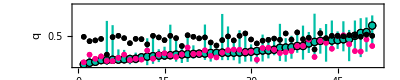

```mathematica
figS=Table[
data=dataS⟦ordernetworks⟧⟦i⟧;
Show[
ListPlot[Thread[{i,data}],
PlotRange->{{0,Length@dataS+1},{0,1}},
PlotStyle->Directive[RGBColor[0, 0.75, 0.65]],
Frame->{True,True,False, False},
FrameTicksStyle->11,
FrameLabel->{"network ID","q","",""},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,None}},
AspectRatio->0.2,
ImageSize->{Automatic,170},
 Joined->True]
,
ListPlot[{{i,data⟦2⟧}},
 PlotStyle->Directive[Black, PointSize[0.015]]]
,
ListPlot[{{i,data⟦2⟧}},
 PlotStyle->Directive[RGBColor[0, 0.75, 0.65], PointSize[0.01]]]
]
,{i,1,Length@dataS}]//Show;

figD=Table[
data=dataD⟦ordernetworks⟧⟦i⟧;
Show[
ListPlot[{{i,data⟦2⟧}},
PlotStyle->Directive[RGBColor[1, 0, 0.54], PointSize[0.01]],
(*PlotRange->{{0,1},{0,Length@dataD+1}},*)
Frame->{True,True,False, False},
FrameTicksStyle->11,
FrameLabel->{"q","network ID","",""},
FrameTicks->{{All,None},{Range[-1,1,0.2],None}},
AspectRatio->GoldenRatio
]
]
,{i,1,Length@dataD}]//Show;

figR=Table[
data=dataR⟦ordernetworks⟧⟦i⟧;
Show[
ListPlot[{{i,data⟦2⟧}},
PlotStyle->Directive[Black, PointSize[0.03]],
(*PlotRange->{{0,1},{0,Length@dataR+1}},*)
Frame->{True,True,False, False},
FrameTicksStyle->11,
PlotMarkers->"OpenMarkers",
FrameLabel->{"q","network ID","",""},
FrameTicks->{{All,None},{Range[-1,1,0.2],None}},
AspectRatio->GoldenRatio
]
]
,{i,1,Length@dataR}]//Show;

Show[ figS,figD,figR]
```

Median q^*across systems

```mathematica
medianR=#⟦2⟧&/@dataR;
medianS=#⟦2⟧&/@dataS;
medianD=#⟦2⟧&/@dataD;

Median[#]&/@{medianR,medianS, medianD};

Count[medianR-medianS,_?(#≥ 0&)]/Length@medianR//N
Count[medianD-medianS,_?(#≥ 0&)]/Length@medianR//N
```

0.921569

0.607843

```mathematica
Min@medianD
Max@medianD
```

0.0666667

0.508197

## Fig 4c r_1

All networks that we analyze

```mathematica
networks=Range@Length@EWS;
```

Calculate the quantiles for (r_1)_sensor across all networks.
Using sensor score

```mathematica
numberofsamples = 300;
ϵ=0.01;

dataS=Table[
CalculateRsensor[networkID, numberofsamples, ϵ]
,{networkID,networks}];
```

```mathematica
Median@dataS
```

{0.266667,0.482759,0.777778}

Using degree

```mathematica
numberofsamples = 300;
ϵ=0.01;

dataD=Table[
CalculateRdegree[networkID, numberofsamples, ϵ]
,{networkID, networks}];
```

At random

```mathematica
numberofsamples = 300;
ϵ=0.01;

dataR=Table[
CalculateRrand[networkID, numberofsamples, ϵ]
,{networkID, networks}];
```

Order

```mathematica
ordernetworks2=Take[#,{2}]&/@dataS//Flatten//Ordering;
```

With ordering by q^*

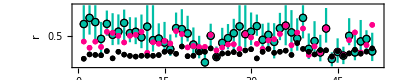

```mathematica
figS=Table[
data=dataS⟦ordernetworks⟧⟦i⟧;
Show[
ListPlot[Thread[{i,data}],
PlotRange->{{0,Length@dataS+1},{0,1}},
PlotStyle->Directive[RGBColor[0, 0.75, 0.65]],
Frame->{True,True,False, False},
FrameTicksStyle->11,
FrameLabel->{"network ID","r","",""},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,None}},
AspectRatio->0.2,
ImageSize->{Automatic,170},
 Joined->True]
,
ListPlot[{{i,data⟦2⟧}},
 PlotStyle->Directive[Black, PointSize[0.015]]]
,
ListPlot[{{i,data⟦2⟧}},
 PlotStyle->Directive[RGBColor[0, 0.75, 0.65], PointSize[0.01]]]
]
,{i,1,Length@dataS}]//Show;

figD=Table[
data=dataD⟦ordernetworks⟧⟦i⟧;
Show[
ListPlot[{{i,data⟦2⟧}},
PlotStyle->Directive[RGBColor[1, 0, 0.54], PointSize[0.01]],
(*PlotRange->{{0,1},{0,Length@dataD+1}},*)
Frame->{True,True,False, False},
FrameTicksStyle->11,
FrameLabel->{"q","network ID","",""},
FrameTicks->{{All,None},{Range[-1,1,0.2],None}},
AspectRatio->GoldenRatio
]
]
,{i,1,Length@dataD}]//Show;

figR=Table[
data=dataR⟦ordernetworks⟧⟦i⟧;
Show[
ListPlot[{{i,data⟦2⟧}},
PlotStyle->Directive[Black, PointSize[0.03]],
(*PlotRange->{{0,1},{0,Length@dataR+1}},*)
Frame->{True,True,False, False},
FrameTicksStyle->11,
PlotMarkers->"OpenMarkers",
FrameLabel->{"q","network ID","",""},
FrameTicks->{{All,None},{Range[-1,1,0.2],None}},
AspectRatio->GoldenRatio
]
]
,{i,1,Length@dataR}]//Show;

Show[ figS,figD,figR]
```

## Fig 4b

```mathematica
data=Flatten[Table[
EWnom=Table[EWS⟦network⟧⟦i⟧//Flatten, {i,1,Length@EWS⟦network⟧}];

SensorScore = SS⟦network⟧;
medianEW = Median@EWnom;

Thread[{medianEW/Max[medianEW],SensorScore}]
,{network,1,Length@EWS}],1];
```

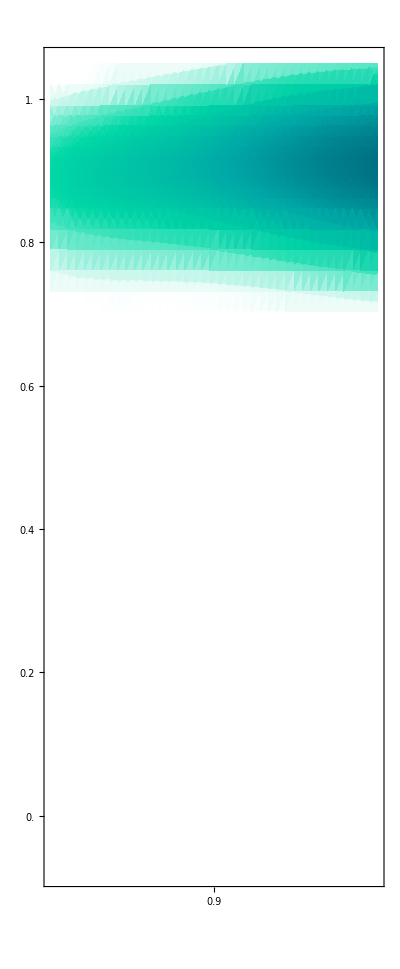

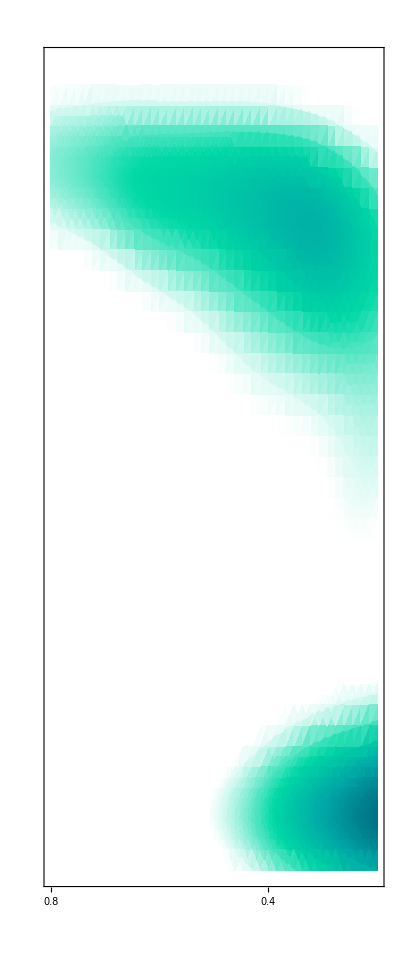

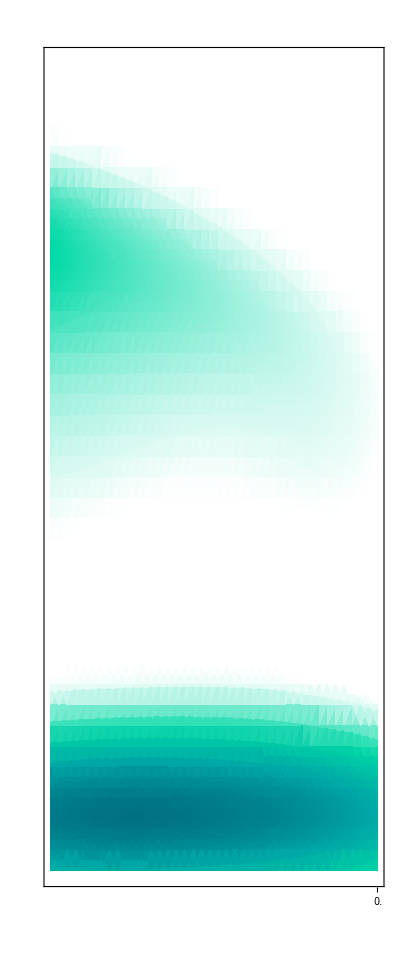

```mathematica
SmoothDensityHistogram[data,Automatic,
ColorFunction->(Blend[{White,White, RGBColor[0, 0.85, 0.65],RGBColor[0, 0.65, 0.65],RGBColor[0, 0.44, 0.51]},Rescale[#,{0,Max@data⟦All,1⟧}]]&),
ScalingFunctions->{"Reverse",Identity},
Mesh->6,
AspectRatio->1.5*GoldenRatio,
ImageSize->{Automatic,230},
PlotRange->{{0.8,1.0}, Automatic},
FrameTicks->{{Range[0,1,0.2],None},{Range[0,1,0.1],None}},
FrameTicksStyle->11,
PlotLegends->Placed[Automatic,Above],
ColorFunctionScaling->True
]

SmoothDensityHistogram[data,Automatic,
ColorFunction->(Blend[{White,White, RGBColor[0, 0.85, 0.65],RGBColor[0, 0.65, 0.65],RGBColor[0, 0.44, 0.51]},Rescale[#,{0,Max@data⟦All,1⟧}]]&),
ScalingFunctions->{"Reverse",Identity},
Mesh->6,
AspectRatio->1.5*GoldenRatio,
ImageSize->{Automatic,230},
PlotRange->{{0.2,0.8}, Automatic},
FrameTicks->{{None,None},{Range[0,1,0.2],None}},
FrameTicksStyle->11,
PlotLegends->Placed[Automatic,Above],
ColorFunctionScaling->True
]

SmoothDensityHistogram[data,
ColorFunction->(Blend[{White,White, RGBColor[0, 0.85, 0.65],RGBColor[0, 0.65, 0.65],RGBColor[0, 0.44, 0.51]},Rescale[#,{0,Max@data⟦All,1⟧}]]&),
ScalingFunctions->{"Reverse",Identity},
Mesh->6,
AspectRatio->1.5*GoldenRatio,
ImageSize->{Automatic,230},
PlotRange->{{0,0.2}, Automatic},
FrameTicks->{{None,None},{Range[0,1,0.1],None}},
FrameTicksStyle->11,
PlotLegends->Placed[Automatic,Above],
ColorFunctionScaling->True
]
```

## Fig 4 d - f

### Fig4d (dimension reduction)

```mathematica
dr=DimensionReduction[Thread[{MaxSS, SkewnessSS}],1,Method->"AutoEncoder"]
σq = dr[Thread[{MaxSS, SkewnessSS}]]//Flatten;
```

DimensionReducerFunction[…]

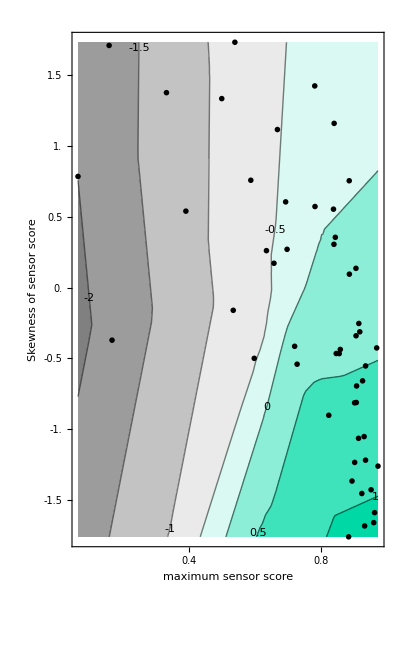

```mathematica
Show[
ContourPlot[dr[{x,y}],{x,Min@MaxSS, Max@MaxSS},{y,Min@SkewnessSS, Max@SkewnessSS},
ImageSize->{Automatic,275},
AspectRatio->GoldenRatio,
ContourLabels->True,
FrameTicksStyle->11,
ColorFunction->(Blend[{Gray,White,RGBColor[0, 0.85, 0.65]},#]&),
FrameLabel->{"maximum sensor score","Skewness of sensor score"},
FrameTicks->{{Range[-2,2,0.5],None},{Range[0,1,0.2],None}},
(*PlotLegends->Placed[BarLegend[
Automatic, 
LabelStyle->{FontSize->11},
 LegendMarkerSize->260, 
(*Ticks->Range[-2,2,0.5],*)
LegendLayout->"Column"],
 Right],*)
ColorFunctionScaling->True
]
,
ListPlot[Thread[{MaxSS, SkewnessSS}],
PlotStyle->Black,
PlotMarkers->"OpenMarkers"
]
]
```

### Fig 4e (q^*-(q^*)_rand)

```mathematica
data = Thread[{σq,ρq, qData}];
(*nlm=NonlinearModelFit[data, a x^2 + e x+ b  x y + c y^2+ f y+ d,{a, b, c , d,e,f},{x,y}]*)
nlm=NonlinearModelFit[data, a x^2 + b y*x + c y^2+ d,{a,b,c,d},{x,y}]
nlm["AdjustedRSquared"]
nlm["ParameterPValues"]
Mean@nlm["MeanPredictionErrors"]
```

FittedModel[-0.421489+0.0908778 x^2-0.000104077 x y+0.0000342726 y^2]

0.765766

{0.000175527,0.759868,0.0745071,0.0000776123}

0.0298887

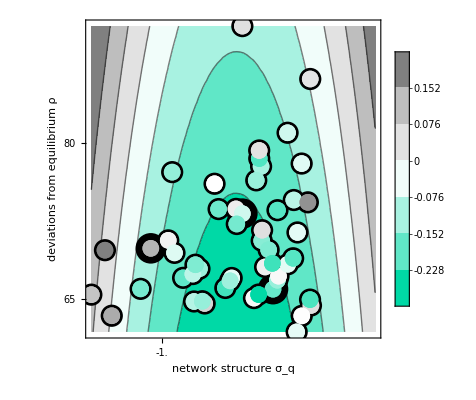

```mathematica
colors=Blend[{RGBColor[0, 0.85, 0.65],White,Gray},Rescale[#,{Min@qData,Max@qData}]]&/@qData;

Show[
ContourPlot[nlm[x,y],{x, Min@σq,2},{y,Min@ρq, Max@ρq},
ImageSize->{Automatic,275},
FrameTicksStyle->11,
Contours->6,
(*Contours->{-0.5,-0.2,-0.171,0.171,0.2,0.5},*)
FrameLabel->{"network structure σ_q","deviations from equilibrium ρ"},
FrameTicks->{{Range[-10,100,5],None},{Range[-10,10,0.5],None}},
(*ColorFunction->(Blend[{RGBColor[0, 0.85, 0.65],White,Gray},Rescale[#,{0,1}]]&),*)
ColorFunction->(Blend[{RGBColor[0, 0.85, 0.65],White,Gray},#]&),
PlotLegends->Placed[BarLegend[
Automatic, 
LabelStyle->{FontSize->11},
 LegendMarkerSize->260, 
(*Ticks->Range[-2,2,0.5],*)
LegendLayout->"Column"],
 Right],
ColorFunctionScaling->True
(*PlotLegends->Automatic*)
]
,
ListPlot[Thread[{σq,ρq}]⟦{2,5,6}⟧,
PlotStyle-> Directive[Black, PointSize[0.055],Opacity[1]]
]
,
ListPlot[Thread[{σq,ρq}],
PlotStyle-> Directive[Black, PointSize[0.04],Opacity[1]]
]
,
ListPlot[Partition[Thread[{σq,ρq}],1],
PlotStyle->(Directive[#,PointSize[0.03]]&/@colors)
]
]
```

### Fig 4f (r_1-r_(1,rand))

```mathematica
Clear[nlm]
data = Thread[{σq,ρq, rData}];
(*nlm=NonlinearModelFit[data, a x^2 + e x+ b  x y + c y^2+ f y+ d,{a, b, c , d,e,f},{x,y}]*)
nlm=NonlinearModelFit[data, a x^4 + b y*x + c y+ d,{a,b,c,d,e},{x,y}]
nlm["AdjustedRSquared"]
nlm["ParameterPValues"]
Mean@nlm["MeanPredictionErrors"]
```

FittedModel[0.776938-0.0263586 x^4-0.00699616 y-0.000188044 x y]

0.678885

{0.0180977,0.742328,0.116007,0.0155896,0.}

0.0461115

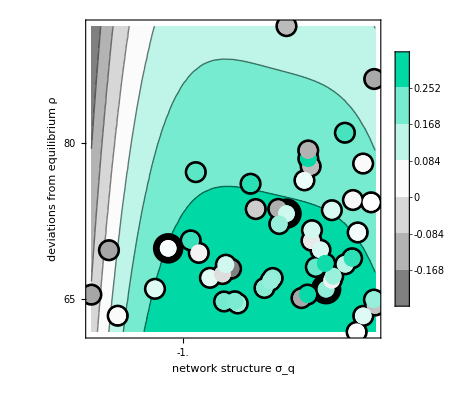

```mathematica
colors=Blend[{Gray,White,RGBColor[0, 0.85, 0.65]},Rescale[#,{Min@rData,Max@rData}]]&/@rData;

Show[
ContourPlot[nlm[x,y],{x, Min@σq, Max@σq},{y,Min@ρq, Max@ρq},
ImageSize->{Automatic,275},
FrameTicksStyle->11,
Contours->6,
(*Contours->{-0.5,-0.2,-0.171,0.171,0.2,0.5},*)
FrameLabel->{"network structure σ_q","deviations from equilibrium ρ"},
FrameTicks->{{Range[-10,100,5],None},{Range[-10,10,0.5],None}},
(*ColorFunction->(Blend[{RGBColor[0, 0.85, 0.65],White,Gray},Rescale[#,{0,1}]]&),*)
ColorFunction->(Blend[{Gray,White,RGBColor[0, 0.85, 0.65]},#]&),
PlotLegends->Placed[BarLegend[
Automatic, 
LabelStyle->{FontSize->11},
 LegendMarkerSize->260, 
(*Ticks->Range[-2,2,0.5],*)
LegendLayout->"Column"],
 Right],
ColorFunctionScaling->True
(*PlotLegends->Automatic*)
]
,
ListPlot[Thread[{σq,ρq}]⟦{2,5,6}⟧,
PlotStyle-> Directive[Black, PointSize[0.055],Opacity[1]]
]
,
ListPlot[Thread[{σq,ρq}],
PlotStyle-> Directive[Black, PointSize[0.04],Opacity[1]]
]
,
ListPlot[Partition[Thread[{σq,ρq}],1],
PlotStyle->(Directive[#,PointSize[0.03]]&/@colors)
]
]
```

## Fig S7

```mathematica
NormDeg =Table[Deg⟦i⟧/Max@Deg⟦i⟧,{i,51}];
```

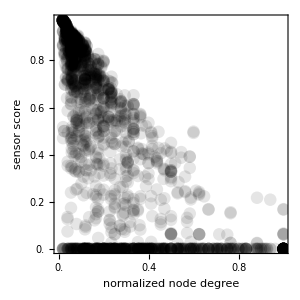

```mathematica
ListPlot[Transpose@{Flatten[NormDeg],Flatten[SS]},
PlotStyle->{Black,PointSize[.03],Opacity[0.1]},
AxesLabel->{"Degree","Sensor Score"},
Frame->True,
AspectRatio->1,
ImageSize->300,
FrameTicksStyle->12,
FrameTicks->{{Range[0,1,0.2],None},{Range[0,1,0.2],None}},
FrameLabel->{"normalized node degree", "sensor score" }]
```